```mathematica
1 / Pi Sum[(-1)^n/ ((n/2)^2 - EE), {n, 0, Infinity}]
```

```mathematica
Sum[(-1)^n (-1)^m / (n ^2 + m^2), {n, 0, Infinity}, {m, 0, Infinity}]
```

∑_(n=0)^∞ ∑_(m=0)^∞ (-1)^(m+n)/(m^2+n^2)

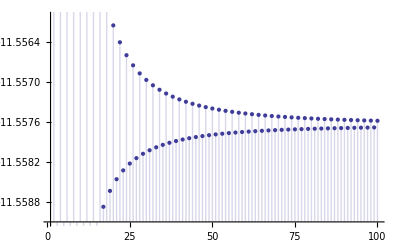

```mathematica
DiscretePlot[Sum[(-1)^n (-1)^m / (n ^2 + m^2 - 0.1), {n, 0, maxnm}, {m, 0, maxnm}], {maxnm, 1, 100}]
```

```mathematica
res[EE_] :=(-1-2 √EE π Csc[2 √EE π])/(2 EE π)
```

```mathematica
res[5]
```

(-1-2 √5 π Csc[2 √5 π])/(10 π)

```mathematica
N[%]
```

-1.45718